```mathematica
OS="win";(*or,linux*)
Needs["ErrorBarPlots`"];
Needs["EDA`"];
If[OS=="win",
Print["Working Directory:,",curDir=SetDirectory["C:\\Users\\Prajwal\\Dropbox\\nEDM\\psi-nedm\\Analysis"]];
Print["(ASCII) Rawdata Directory:,",AscDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\rawdata"];
];
If[OS=="linux",
Print["Working Directory:",curDir=SetDirectory["/home/prajwal/Dropbox/nEDM/psi-nedm/Analysis"]];
Print["(faster) Rawdata Directory:",fastDir="/home/prajwal/nEDM/rawdata"];
Print["(ASCII) Rawdata Directory:",AscDir="/home/prajwal/Dropbox/nEDM/rawdata"];
];
Print["Runs in the list: runNum = ",runNum={10195,10199,10207}]
(*2016:{11149,11154,11159,11162,11166,11170,11205,11208,11213,11214,11218,11219,11239,11243,11247,11250,11255,11263,11267,11270,11272,11276,11277,11281,11289,11292,11295,11299,11305,11325,11331,11334,11342,11348,11351,11354,11357,11360,11363,11366,11385,11388,11391,11395,11398,11399,11402,11405,11406,11409,11412,11416,11430,11433,11436,11439,11442,11445,11448,11453,11457,11461,11464},
{11149,11154,11159,11162,11166,11170,11205,11213,11214,11218,11219,11239,11243,11247,11250,11255,11263,11267,11270,11272,11276,11277,11281,11289,11292,11295,11299,11305,11325,11334,11342,11348,11351,11354,11360,11363,11366,11385,11388,11391,11395,11398,11399,11402,11405,11406,11409,11412,11416,11430,11433,11436,11439,11442,11445,11448,11453,11457,11461,11464},
2015:{10210,10219,10224,10227,10231,10239,10246,10261,10262,10264,10265,10270,10271,10273,10276,10281,10284,10286,10297,10345,10353,10357,10358,10386,10390,10391,10400,10404,10413,10415,10417,10420,10450,10451,10453,10455,10462,10463,10465,10469,10471,10472,10476,10483,10497,10541}]*)
(*Using command:$ sed'/#/d'./010195-0_UCNswitch.edm>mody.edm,*)
Print["#Runs in the list: runn = ",runn=Dimensions[runNum][[1]]];
metaStructure={Real,Word,Real,Real,Real,Real,Real};
metaStructure2={Word,Real,Real,Word,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real};
histbeg=100;histlast=1400;icycle=25;ChNum=4;binw=10;
histbeg2=0;
ptreal=Table[0,{k,1,runn}];
ptdat=0;
ptdat2=0;
(*6->HV, SF1->25, SF2->26,U->27,D->28,U+D->27+28,Monitor->30,TotN->32,Fill->31,RF->-1*)
```

Working Directory:,C:\Users\Prajwal\Dropbox\nEDM\psi-nedm\Analysis

(ASCII) Rawdata Directory:,C:\Users\Prajwal\Dropbox\nEDM\rawdata

Runs in the list: runNum = {10195,10199,10207}

#Runs in the list: runn = 3

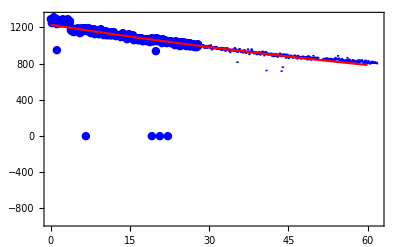

```mathematica
runnum=runNum[[3]];
data=ReadList[StringJoin[AscDir,"\\",IntegerString[runnum,10,6],"\\",IntegerString[runnum,10,6],"_Meta3.edm"],metaStructure2];
dataswt=Import[StringJoin[AscDir,"\\",IntegerString[runnum,10,6],"\\",IntegerString[runnum,10,6],"-0_UCNswitch3.edm"]];
maxcy2=Dimensions[dataswt][[1]];
maxcy=data[[-1]][[2]];
ptdat2=Table[{(AbsoluteTime[dataswt[[k]][[1]]]-AbsoluteTime[dataswt[[1]][[1]]])/(3600),{dataswt[[k]][[2]],0}},{k,1,maxcy2}];
ptdat=Table[{(AbsoluteTime[data[[k]][[1]]]-AbsoluteTime[dataswt[[1]][[1]]])/(3600),{(data[[k]][[27]]+data[[k]][[28]])/10,Sqrt[data[[k]][[27]]+data[[k]][[28]]]/10}},{k,1,maxcy}];
Show[{EDAListPlot[ptdat,ptdat2,PlotLegends->{"UCN # × 10","Switch Position"},PlotStyle->{Blue,Red},PlotRange->Full,Frame->True,PlotRange->Full,FrameLabel->{"Time (Hours)","UCN # × 10, Switch Position"},TicksStyle->Directive[FontSize->40],LabelStyle->{18},ImageSize->{1000},PlotMarkers->{Automatic,Medium}],
Plot[{1230(Exp[-0.0075t])},{t,0,60},PlotStyle->{Blue,Red},Frame->True,FrameLabel->{"Time (Hours)","UCN # × 10 , Switch Position"},TicksStyle->Directive[FontSize->40],LabelStyle->{18},ImageSize->{1000},Axes->False]}]
```

Sorting Matches, Dimensions[ptdatcorr][[1]] = 259 == Dimensions[ptdat2corr][[1]] = 259

Average position of filling switch: avgswitchpos = 233.721

Size of sorted sets: newmaxcy = 259

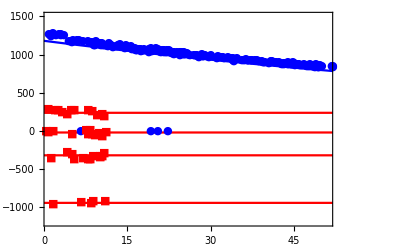

```mathematica
j=1;i=1;ptdatcorr={};ptdat2corr={};
diffswt={};diffud={};avgswitchpos=0;
While[((i≤maxcy)&&(j≤maxcy2)),
randnum=RandomReal[];
If[(((ptdat[[i]][[1]]-ptdat2[[j]][[1]])<(300/(3600)))&&(ptdat2[[j]][[2]][[1]]<-200)&&(ptdat2[[j]][[2]][[1]]>-600)),
ptdatcorr=AppendTo[ptdatcorr,{ptdat[[i]][[1]],{N[ptdat[[i]][[2]][[1]]],ptdat[[i]][[2]][[2]]}}];
ptdat2corr=AppendTo[ptdat2corr,{ptdat2[[i]][[1]]*5,{N[ptdat2[[i]][[2]][[1]]-(randnum*100)+50],0}}];
];
If[((ptdat[[i]][[1]]-ptdat2[[j]][[1]])≥(300/(3600))),
j++;,
If[((ptdat[[i]][[1]]-ptdat2[[j]][[1]])≤-(300/(3600))),
i++;,
i++;j++;
];
];
];
If[Dimensions[ptdatcorr][[1]]==Dimensions[ptdat2corr][[1]],
Print["Sorting Matches, Dimensions[ptdatcorr][[1]] = ",Dimensions[ptdatcorr][[1]]," == Dimensions[ptdat2corr][[1]] = ",Dimensions[ptdat2corr][[1]]]
,
Print["!!!!Sorting does NOT Matches, Dimensions[ptdatcorr][[1]] = ",Dimensions[ptdatcorr][[1]]," == Dimensions[ptdat2corr][[1]] = ",Dimensions[ptdat2corr][[1]]]
];
Print["Average position of filling switch: avgswitchpos = ",avgswitchpos=(-Mean[ptdat2corr[[;;,2]][[;;,1]]]-20)];
Print["Size of sorted sets: newmaxcy = ",newmaxcy=Dimensions[ptdatcorr][[1]]];
fitucnnum=Interpolation[ptdatcorr[[100;;,2]][[;;,1]],InterpolationOrder->2];
For[i=1,i≤newmaxcy,i++,
randnum=RandomReal[];
diffswt=AppendTo[diffswt,{ptdat2corr[[i]][[1]],{0.1*N[(ptdat2corr[[i]][[2]][[1]]-avgswitchpos)],0}}];
diffud=AppendTo[diffud,{ptdatcorr[[i]][[1]],{-10*Abs[(ptdatcorr[[i]][[2]][[1]]-(1230(Exp[-0.0075(i/10)])-50))/(1230(Exp[-0.0075(i/10)])-50)],N[10*ptdatcorr[[i]][[2]][[2]]/(1230(Exp[-0.0075(i/10)])-50)]}}];
];
ptdat3=Transpose[{diffswt[[;;,2]][[;;,1]],Transpose[{diffud[[;;,2]][[;;,1]]*0.1+0.1,diffud[[;;,2]][[;;,2]]}]}];
Show[{
(*Plot[fitucnnum[xx*10],{xx,1,newmaxcy/10},PlotRange->{{1,62},{-300,1500}},Frame->True,PlotRange->Full,FrameLabel->{"Time (Hours)","UCN # × 10, Switch Position"},TicksStyle->Directive[FontSize->40],LabelStyle->{18},ImageSize->{1000}]*)
Plot[{1230(Exp[-0.0075t])-50,avgswitchpos,-25,-325,-950},{t,0,60},PlotRange->{{1,51},{-1200,1500}},PlotStyle->{Blue,Red,Red,Red,Red},Frame->True,FrameLabel->{"Time (Hours)","UCN # × 10 , Switch Position"},TicksStyle->Directive[FontSize->40],LabelStyle->{18},ImageSize->{1000},Axes->False],
EDAListPlot[ptdatcorr,ptdat2corr,PlotLegends->{"(N_Up + N_Down) × 10","Switch Position"},PlotStyle->{Blue,Red},PlotRange->{{1,51},{-1200,1500}},Frame->True,FrameLabel->{"Time (Hours)","(N_Up + N_Down) × 10 , Switch Position"},TicksStyle->Directive[FontSize->40],LabelStyle->{18},ImageSize->{1000},PlotMarkers->{Automatic,Medium}]
}]
```

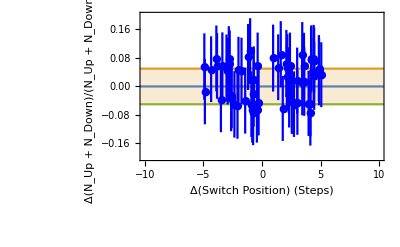

```mathematica
Show[{Plot[{0,0.05,-0.05},{xx,-100,100},PlotRange->{{-10,10},{-0.2,0.2}},Filling->{2->{3}},Frame->True,FrameLabel->{"Δ(Switch Position) (Steps)","Δ(N_Up + N_Down)/(N_Up + N_Down) (%)"},TicksStyle->Directive[FontSize->40],LabelStyle->{18,Black},ImageSize->{1000}],
EDAListPlot[ptdat3,PlotStyle->{Blue,Red},PlotRange->{{-100,100},{-1,0.2}},Frame->True,FrameLabel->{"Δ(Switch Position) (Steps)","-Δ(N_Up + N_Down)/(N_Up + N_Down) (%)"},TicksStyle->Directive[FontSize->40],LabelStyle->{18,Black},ImageSize->{1000},PlotMarkers->{Automatic,Medium}]
}]
```

## Extras

{a→1212.67,k→0.0686385}

1212.67

b

0.0686385

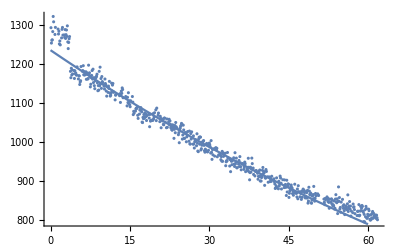

```mathematica
fitucnnum=FindFit[Transpose[{ptdatcorr[[100;;,1]]/10,ptdatcorr[[100;;,2]][[;;,1]]}],a(Exp[-k t]),{{a,1200},{k,0.0068}},t]
a/.fitucnnum
b/.fitucnnum
k/.fitucnnum
Show[{
ListPlot[Transpose[{ptdatcorr[[;;,1]],ptdatcorr[[;;,2]][[;;,1]]}]],
Plot[1230(Exp[-0.0075t])+5,{t,0,60}]
}]
```